# 复变函数和流体力学

```mathematica
SetOptions[EvaluationNotebook[],CommonDefaultFormatTypes->{"Output"->StandardForm}]
```

## 势函数和流函数

### Φ=a+ibz

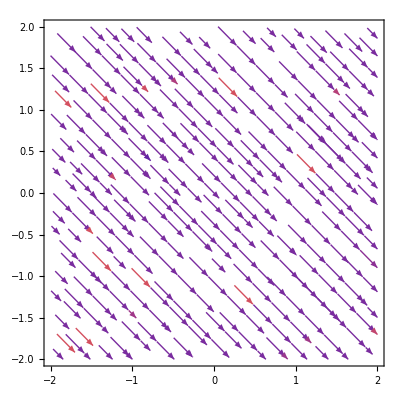

```mathematica
phi=Exp[I Pi/4] z;
ComplexStreamPlot[Conjugate[D[phi,z]],{z,-2-2 I,2+2 I},StreamPoints->Automatic]
```

### Φ=Log[z]

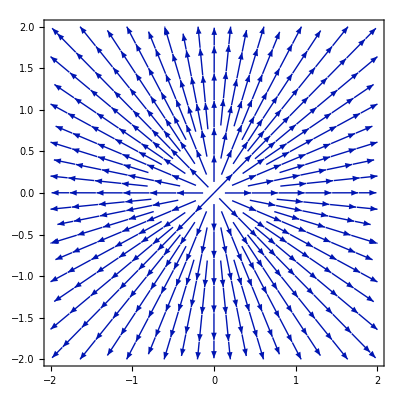

```mathematica
phi=Log[z];
ComplexStreamPlot[Conjugate[D[phi,z]],{z,-2-2 I,2+2 I},StreamPoints->Automatic]
```

### Φ=iLog[z]

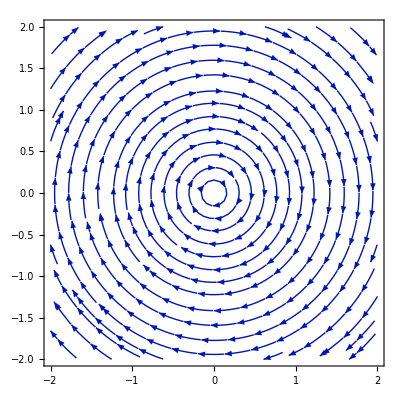

```mathematica
phi=I Log[z];
ComplexStreamPlot[Conjugate[D[phi,z]],{z,-2-2 I,2+2 I},StreamPoints->Automatic]
```

### 绕圆柱体的复势

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

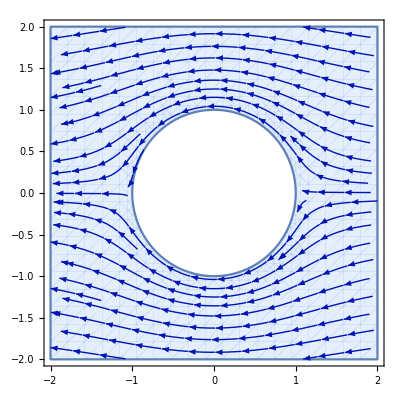

```mathematica
phi=z Conjugate[u]+r^2/z u-I G/(2 Pi)*Log[z]/.r->1/.u->-1/.G->0;
ComplexStreamPlot[Conjugate[D[phi,z]],{z,-2-2 I,2+2 I},StreamPoints->Automatic,RegionFunction->Function[{z,f},Abs[z]>1]]
```

```mathematica
shift=0.15+I*0.2;
```

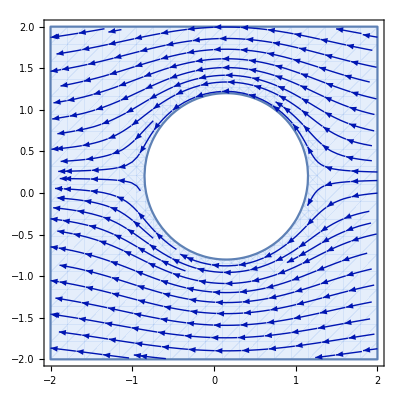

```mathematica
phi=z Conjugate[u]+r^2/z u-I G/(2 Pi)*Log[z]/.z->z-shift/.r->1/.u->-1/.G->0;
ComplexStreamPlot[Conjugate[D[phi,z]],{z,-2-2 I,2+2 I},StreamPoints->Automatic,RegionFunction->Function[{z,f},Abs[z-shift]>1]]
```

## 茹可夫斯基变换

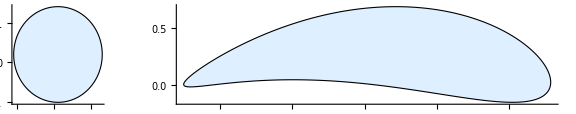

```mathematica
(*Parameters for the circle in the z-plane*)c=1.0; (*Parameter controlling the airfoil thickness*)
R=1.2; (*Radius of the circle (must be>c for a proper airfoil)*)
centerOffset={0.1,0.2}; (*Offset of the circle's center from the origin*)

(*Define the circle in the z-plane*)
circle[t_]:=centerOffset+R {Cos[t],Sin[t]};
circlepoint=circle/@Range[0,2 Pi,0.01];
(*Joukowski transformation*)
joukowski[{x_,y_}]:=Module[{z,zeta},z=x+I y;
zeta=z+c^2/z;(*Joukowski transformation*){Re[zeta],Im[zeta]}];

(*Apply the Joukowski transformation to the circle*)
airfoilPoints=joukowski/@circle/@Range[0,2 Pi,0.01];

circlePlot=Graphics[{EdgeForm[Black],(*Optional:Add a black border*)LightBlue,(*Fill color*)Polygon[circlepoint]          (*Define the polygon using the points*)},Axes->True              (*Optional:Show axes*)];

airfoilPlot=Graphics[{EdgeForm[Black],(*Optional:Add a black border*)LightBlue,(*Fill color*)Polygon[airfoilPoints]          (*Define the polygon using the points*)},Axes->True              (*Optional:Show axes*)];

(*Show both plots side by side*)
GraphicsRow[{circlePlot,airfoilPlot},ImageSize->Large]
```

## 机翼流线

```mathematica
shift=0.15+I*0.2;
```

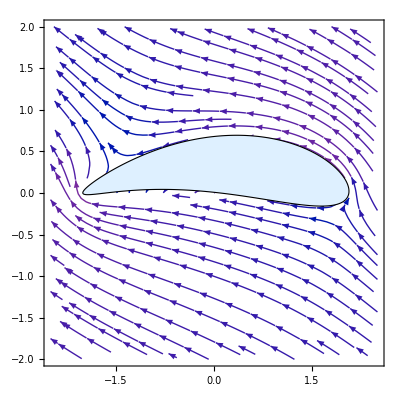

```mathematica
phi=z Conjugate[u]+r^2/z u-I G/(2 Pi)*Log[z]/.z->z-shift/.z:>If[Re[z]<0, 1/2 (z-√(-4 c^2+z^2)),1/2 (z+√(-4 c^2+z^2))]/.r->R/.u->-1 Exp[-I Pi/6] /.G->0;
jplot=ComplexStreamPlot[Conjugate[D[phi,z]],{z,-2.5-2 I,2.5+2 I},StreamPoints->Automatic,PerformanceGoal->"Quality"];
Show[jplot,airfoilPlot]
```

```mathematica
Manipulate[Module[{phi,dPhiDz},phi=z Conjugate[u]+r^2/z u/. z->z-shift/. z:>If[Re[z]<0,1/2 (z-Sqrt[-4 c^2+z^2]),1/2 (z+Sqrt[-4 c^2+z^2])]/. r->R;
phi=phi/. u-> -Exp[I*uPhase];
dPhiDz=Conjugate[D[phi,z]];
jplot=ComplexStreamPlot[dPhiDz,{z,-2.5-2 I,2.5+2 I},StreamPoints->Automatic,PerformanceGoal->"Quality",StreamScale->0.15];
Show[jplot,airfoilPlot]],{{uPhase,Pi/6,"Phase of u"},0,2 Pi,Appearance->"Labeled"}]
```